Dimensions: {25025,2}

Dimensions: {33310,2,2}

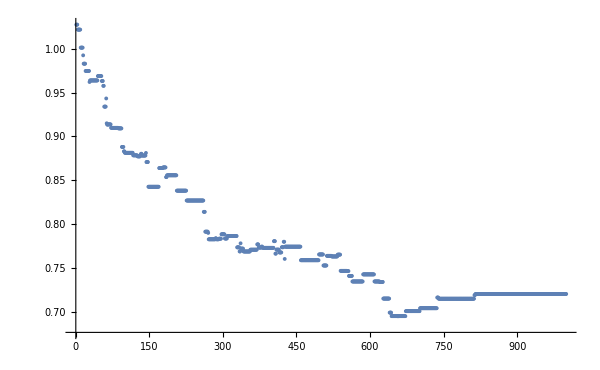

```mathematica
{energies,volumes}=Transpose@Import[NotebookDirectory[]<>"out/x64-Release/output-info.txt","Table"];

{fillings,iterations}=LoadCube[NotebookDirectory[]<>"out/x64-Release/output-filling.binary"];
emptyDisks=Table[Disk[{x,y},0.1],{x,0,20},{y,0,20}];
filledDisks=Map[Disk[#,0.1]&,fillings,{2}];

{edges,iterations}=LoadCube[NotebookDirectory[]<>"out/x64-Release/output-boundary.binary"];

Manipulate[
Graphics[{LightGray,emptyDisks,Brown,filledDisks[[i]],Line[edges[[i]]]},ImageSize->600,Frame->True],{i,1,Length@iterations,1}]

ListPlot[{energies},PlotRange->All]
```

```mathematica
LoadCube[filename_]:=Module[{d,dims,s,blockData,annotations,sectionSizes},
file = OpenRead[filename, BinaryFormat->True];
d=First@BinaryReadList[file, "UnsignedInteger64",1];
dims=BinaryReadList[file, "UnsignedInteger64",d];
Print["Dimensions: ",dims];
s=First@BinaryReadList[file, "UnsignedInteger64",1];
blockData=BinaryReadList[file, "Real64",Times@@dims];
annotations=BinaryReadList[file, "Real64",s];
sectionSizes=BinaryReadList[file, "Integer32",s];
Close[file];
{TakeList[ArrayReshape[blockData,dims],sectionSizes],annotations}]
```

```mathematica
(*Particle Indices are: x,y, velX,velY, dens, press, intEnergy, kinEnergy, Dummy, group, id*)
(*Solid Indices are: x,y, velX,velY, angle, angVel, dragForce, group*)
```

Dimensions: {549,9}

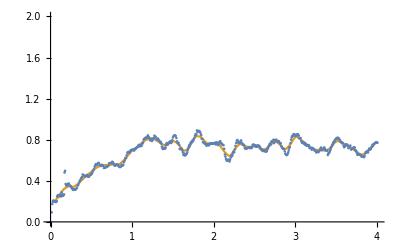

0.743187

```mathematica
(*Show the drag force*)
{solids,times}=LoadCube[NotebookDirectory[]<>"out/x64-Release/solids.binary"];
drags=Transpose[{times,solids[[All,1,7]]}];
ListPlot[{drags,MovingAverage[drags,20]},PlotRange->{All,{0,2}},Joined->{False, True}]
Mean@Cases[drags,{t_,d_}/;t>1->d]
```

```mathematica
{partics,times}=LoadCube[NotebookDirectory[]<>"out/x64-Release/particles.binary"];
groupCols={RGBColor[0.49, 0.63, 0.96],Black};
Manipulate[Graphics[{groupCols[[#[[10]]+1]],Disk[#[[{1,2}]],0.005]}&/@partics[[i]], PlotRange->{{0,1},{0,0.6}},Frame->True,AspectRatio->Automatic,ImageSize->600],{i,1,Length@partics,1}]
```

Dimensions: {67926,12}

Dimensions: {67926,12}

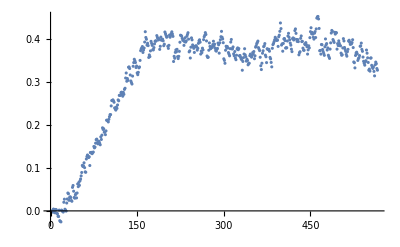

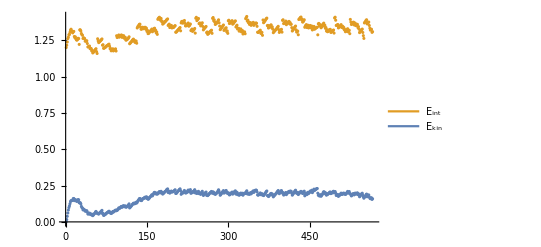

```mathematica
{partics, times}=LoadCube[NotebookDirectory[]<>"out/x64-Release/particles.binary"];

ListPlot[Total[partics[[All,All,3]],{2}]/Length/@partics,PlotRange->All]
ListPlot[{Total[partics[[All,All,8]],{2}],Total[partics[[All,All,7]],{2}]},PlotLayout->"Stacked",PlotLegends->{"E_kin","E_int"}]
```

```mathematica
Manipulate[ListDensityPlot[{#[[1]],#[[2]],#[[5]]}&/@partics[[i]], PlotRange->{{0,1},{0,0.6},All},
Mesh->All,InterpolationOrder->0,ColorFunction->ColorData[{"Rainbow",{0.5,2.0}}],ColorFunctionScaling->False,ClippingStyle->Automatic,
PlotLegends->Automatic,Frame->True,AspectRatio->Automatic,ImageSize->600],{i,1,Length@partics,1},TrackedSymbols:>{i}]
```